# Connected Components Decomposition

Find components in an image and convert them to a graph. The steps involved include:

Quantization: reduce the number of colors to limit the number of components

Connected Components: find all the particles

Decomposition: create a graph with each component as a node and edges between adjacent nodes

## Import Image

```mathematica
image=Import["/Users/dvs/Projects/iProcessor/test/EO_27.jpg"]
```

-Graphics-

## Color Quantize

```mathematica
quantizedImage=ColorQuantize[image,8,Dithering->False]
```

-Graphics-

## Segment

```mathematica
segmentedImage=ImageSegmentationComponents[quantizedImage,PerformanceGoal->"Quality"]
```

```mathematica
segmentedImage//Colorize
```

-Graphics-

## Find Connected Components

```mathematica
components=ComponentMeasurements[segmentedImage
,{"Area"
,"FilledCircularity"
,"Neighbors"
,"EmbeddedComponents"
,"EmbeddedComponentCount"
,"Label"}
,#Area>10&
,"ComponentAssociation"];
```

## Create Graph

### Edges

```mathematica
edges={};
Do[
If[components[i]⟦5⟧>0,
Do[
AppendTo[edges,
components[i]⟦6⟧->components[i]⟦4,j⟧
];
,{j,components[i]⟦5⟧}
];
]
,{i,Length[components]}
]
```

### Vertices

```mathematica
vertexLabels={};
Do[
If[components[i]⟦5⟧>0,
AppendTo[vertexLabels,Labeled[i,Round[components[i]⟦1⟧]]];
];
,{i,Length[components]}
]
```

### Graph

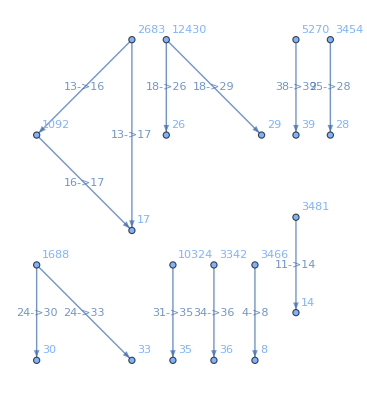

```mathematica
graph=Graph[vertexLabels,edges,VertexLabels->Automatic,EdgeLabels->Automatic]
```

```mathematica
{"Area"
,"FilledCircularity"
,"Neighbors"
,"EmbeddedComponents"
,"EmbeddedComponentCount"
,"Label"}
```

### Underlying Data

```mathematica
ds=Dataset[components];
ds[All,<|"Area"->#[[1]],"FilledCircularity"->#[[2]],"Neighbors"->#[[3]],"EmbeddedComponents"->#[[4]],"EmbeddedComponentsCount"->#[[5]],"Label"->#[[6]]|>&]
```